```mathematica
(* Objects *)
lightLocations={{{300,2000},x},{{1500,2000},y},{{2700,2000},z}};
sensorLocations={{{600,0},400},{{1800,0},700}};
(* Helper Method *)
CalcDistance[a_,b_]:=EuclideanDistance[a,b];
CalcAngle[a_,b_]:=ArcTan[b[[2]]-a[[2]],b[[1]]-a[[1]]];(* 90Degree-Abs[ArcTan[(a[[2]]-b[[2]])/(a[[1]]-b[[1]])]]; *)
(* Object Helper Method *)
LightLocation[a_]:=a[[1]];
LightCd[a_]:=a[[2]];
SensorLocation[a_]:=a[[1]];
SensorExpectLx[a_]:=a[[2]];
```

```mathematica
DrawMap:=Module[{
lights=Function[x,Point[LightLocation[x]]]/@lightLocations,
sensors=Function[x,Point[SensorLocation[x]]]/@sensorLocations,
background=Rectangle[{0,0},{3100,2000}],
lines=Line/@Tuples[{LightLocation/@lightLocations,SensorLocation/@sensorLocations}],
},Show[Graphics[{
LightGreen,background,
Black,lines,
Red,PointSize[0.015],lights,
Blue,sensors
}],
ImageSize->1000,Frame->True,LabelStyle->Large]
];
(* Single *)
```

```mathematica
CalcLx[sensor_,light_]:=(Cos[CalcAngle[SensorLocation[sensor],LightLocation[light]]]*LightCd[light])/(CalcDistance[SensorLocation[sensor],LightLocation[light]]/1000)^2;
CalcError[sensor_,lights_]:=SensorExpectLx[sensor]-Total[Function[light,CalcLx[sensor,light]]/@lights];
```

```mathematica
(* Multiple *)
CalcErrors[sensors_,lights_]:=Function[sensor,CalcError[sensor,lights]]/@sensors;
```

```mathematica
(* Optimize *)
NMinimize[{Mean[Function[x,x^2]/@CalcErrors[sensorLocations,lightLocations]],0≤x,0≤y,0≤z},{x,y,z}]
NMinimize[{Mean[Function[x,x^2]/@CalcErrors[sensorLocations,lightLocations]]+Total[{x,y,z}],0≤x,0≤y,0≤z},{x,y,z}]
```

{8.03195×10^-18,{x→259.759,y→574.059,z→2784.7}}

{3349.73,{x→2.34578×10^-8,y→1215.84,z→2106.36}}

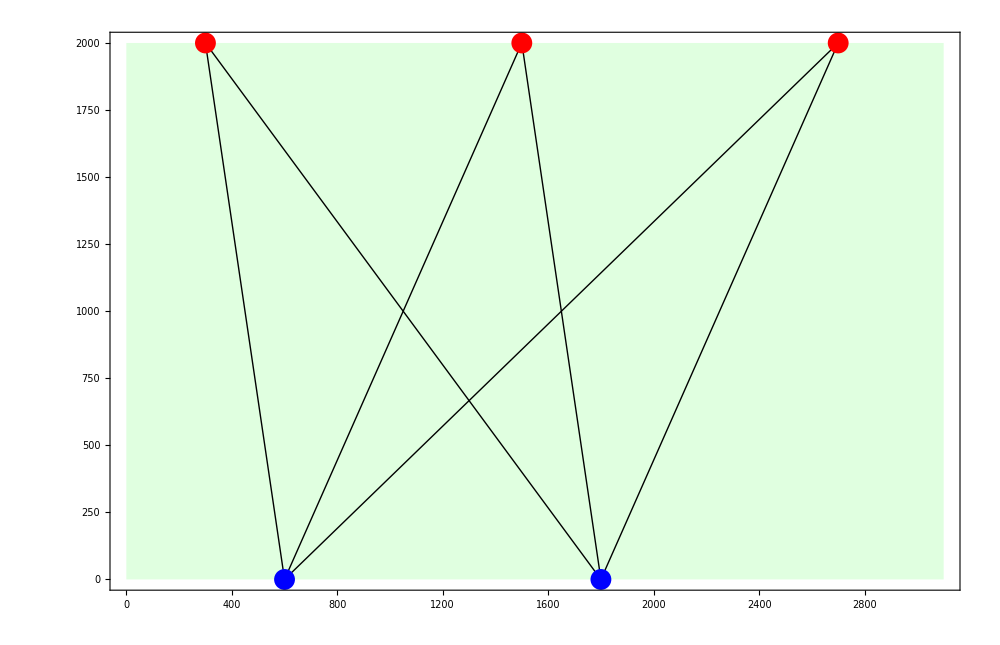

```mathematica
DrawMap
```